# Math 223: Homework 10

Ali Heydari

April. 21st, 2021

Collaborators: Matteo Polimeno, Alex Ho

## Problem 1

Use boundary-layer theory to find a uniform approximation with error of order ϵ^2 for the problem:

				

, 	

Notice that there is no boundary layer in leading order, but one does appear in next order. Compare your solution with the exact solution to this problem.

To find the boundary layer, we can take a look at the coefficient of the first order derivative, i.e. , which is greater than 0. This means that our boundary layer will be at the left boundary, so now solving for the outer layer:



Now substituting this back into the original perturbed ODE, we get that:

 and 

from which we find that  and using the fact that . We can show this with Mathematica:

```mathematica
DSolve[{Subscript[y, 0]'[x]+Subscript[y, 0][x]==0,Subscript[y, 0][0]==E},Subscript[y, 0][x],x]
```

{{y_0[x]→ⅇ^(1-x)}}

So our solution for up to order ϵ is :



We can now continue to find the order ϵ^2 approximation, meaning :

```mathematica
DSolve[{Subscript[y, 1]'[x]+Subscript[y, 1][x]==Exp[1-x],Subscript[y, 1][1]==0},Subscript[y, 1][x],x]
```

{{y_1[x]→ⅇ^(1-x) (-1+x)}}

So putting the first two order solutions together, we get:



Now to find the distinguished limit we can solve for the stretch coordinate in a general form to be:



  

which yields to:



and since we want to make sure that the second order derivative does not vanish, we must have that , which means that . That means that X = x/ϵ.

So we find that the stretch coordinate must be , which yields :



assuming the same solution type as outer solution (i.e. ), we find the first order solution to be:


Now we can do the substitution that , so now we can solve:

```mathematica
DSolve[{Subscript[u, 0]'[X]+Subscript[u, 0][X]==0},Subscript[u, 0][X],X]
```

{{u_0[X]→ⅇ^-X C[1]}}

finding that 

Now using the boundary condition , we can obtain the first order inner solution to be: 




to obtain the next order solution, we can follow the same procedure and get:

```mathematica
DSolve[{Subscript[u, 0]'[X]+Subscript[u, 0][X]== C[1](1-Exp[-X]) + E},Subscript[u, 0][X],X]
```

{{u_0[X]→ⅇ^-X (ⅇ^(1+X)+ⅇ^X C[1]-X C[1])+ⅇ^-X C[2]}}

so the inner solution now becomes:

To determine the constants for the inner solution, we will do the asymptotic matching:

 → 

meaning that  and , so now the inner solution becomes: 



Finally, to find the uniform solution:





and after doing the calculations, we arrive at:

 + 

Now to compare with the exact solution:

```mathematica
NumericalSolution =NDSolve[{0.01 y''[x]+ y'[x]+y[x]==0,y[0]==E,y[1]==1},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
AsymptoticApproximation[x_,ϵ_] = Exp[1-x]*(1 + ϵ*(1-x-Exp[-1/ϵ]))
```

```mathematica
ⅇ^(1-x) (1+(1-ⅇ^(-1/ϵ)-x) ϵ)
```

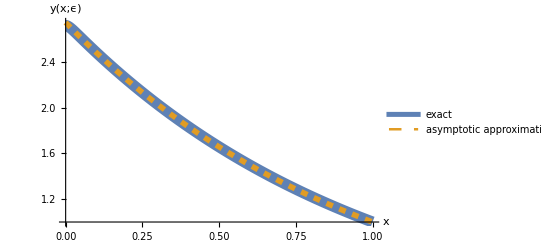

```mathematica
Plot[{y[x]/.NumericalSolution,AsymptoticApproximation[x,0.01]},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 2

Use boundary-layer methods to find an approximate solution to the initial-value problem

					

,

Show that the leading-order uniform approximation satisfies , but not  for arbitrary . Compare the leading-order uniform approximation with the exact solution to the problem when  and  are constants.

As before, we can take a look at the coefficient of the first order derivative, and since we have that , which means that our boundary layer will be at the left boundary. Solving for the outer layer, we take the following form for  : 



Now substituting this back into the original perturbed ODE, we can look at the first order as

```mathematica
DSolve[{a[x]*Subscript[y, 0]'[x]+b[x]*Subscript[y, 0][x]==0,Subscript[y, 0][1]==1},Subscript[y, 0][x],x, Assumptions->{a[x] > 0, b[x]>0,x≥0}]
```

{{y_0[x]→ⅇ^(-b[K[1]]/a[K[1]]K[1]1x)}}

Now we see that this will give us a very ugly solution for . So maybe we should choose nice functions for . If we let . But for now, we will just keep the actual form:



So we have found the leading behavior for .

Finding :

Now for calculating , based on the previous example, we take the stretch coordinate ; in other words we can solve for the stretch coordinate in a general form to be:


  

which yields to:



and since we want to make sure that the second order derivative does not vanish, we must have that , which means that . 

Now that we have found the correct distinguished limit, we can proceed:



So solving for the second order, we obtain:

```mathematica
DSolve[{Subscript[u, 0]''[X] + a[x]*Subscript[u, 0]'[X]==0, Subscript[u, 0][0]==1, Subscript[u, 0]'[0]==1},Subscript[u, 0][X],X] \\ FullSimplify
```

```mathematica
{{Subscript[u, 0][X]->(ⅇ^(-X a[x]) (-1+ⅇ^(X a[x])+ⅇ^(X a[x]) a[x]))/a[x]}}
```

So we get that the first solution to be . We will stop at this leading order approximation for .

Now to find the overlap and do the asymptotic matching:

 → 

 → 

So then we find that

so now that we have found the asymptotic matching, we can write the uniform solution as: 



replacing  with  we get:

Now to see how well our solutions match:

```mathematica
NumericalSolution =NDSolve[{0.1y''[x]+ y'[x]+y[x]==0,y[0]==1,y'[0]==1},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
AsymptoticApproximation[x_,ϵ_] =  - Exp[-x/ϵ] + Exp[-x]+(1/ϵ)
```

ⅇ^-x-ⅇ^(-x/ϵ)+1/ϵ

```mathematica
AsymptoticApproximation[x_,ϵ_] = - E^(-x/ϵ) + 2 + E*(E^(x-1)) - E
```

2-ⅇ+ⅇ^x-ⅇ^(-x/ϵ)

```mathematica
Plot[{y[x]/.NumericalSolution,AsymptoticApproximation[x,0.1]},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

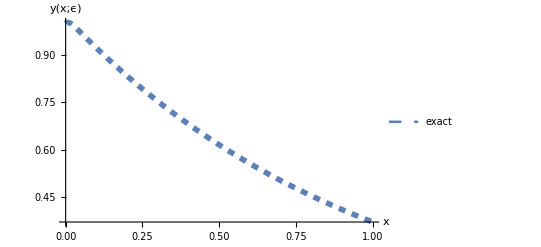

```mathematica
Plot[{y[x]/.NumericalSolution},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 3

The function  satisfies:

		

and is subject to boundary conditions   and  . Find two terms in the outer approximation, applying only the boundary condition at . Next, find two terms in the inner approximation for the boundary layer near , which can be assumed to have width , and only applying the boundary condition at . Finally determine the constants of integration in the inner approximation by matching.

As before, we will start by the outer solution: The leading order is given via:



which just gives us . Now moving on to the second order solution, we can find that using:

```mathematica
DSolve[{Subscript[y, 1]'[x]+Subscript[y, 1][x]==0,Subscript[y, 1][0]==0},Subscript[y, 1][x],x]
```

{{y_1[x]→0}}

which is interesting. So now we want to move on to the inner solutions: for the first order inner solution, we find that

```mathematica
DSolve[{Subscript[Y, 0]''[X]+Subscript[Y, 0]'[X]==0,Subscript[Y, 0][0]==0},Subscript[Y, 0][X],X]
```

{{Y_0[X]→ⅇ^-X (-1+ⅇ^X) C[1]}}

```mathematica
DSolve[{Subscript[Y, 1]''[X]+Subscript[Y, 1]'[X]==-Exp[-X]-(1-Exp[-X]),Subscript[Y, 1][0]==0},Subscript[Y, 1][X],X]
```

{{Y_1[X]→-ⅇ^-X (ⅇ^X X+C[1]-ⅇ^X C[1])}}

Now to find the constant, we can do the asymptotic matching in the limits: 

 → 

 → 

 → 

Now to be able to do the matching for the inner solution, we can look at the series expansion of :



now rewriting the limit we get: 



So we find that . So for the leading order solution, we get: 



and for the solution with two terms we obtain:



Now we will plot these solutions against the numerical solution:

```mathematica
NumericalSol =NDSolve[{0.01*y''[x]+(1+0.01)*y'[x]+y[x]==0,y[0]==0,y[1]==Exp[-1]},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
AsymptoticApproxO1[x_,ϵ_] =  - Exp[-x/ϵ] + Exp[-x]
```

ⅇ^-x-ⅇ^(-x/ϵ)

```mathematica
AsymptoticApproxO2[x_,ϵ_] =  - Exp[-x/ϵ] + Exp[-x] - x
```

ⅇ^-x-ⅇ^(-x/ϵ)-x

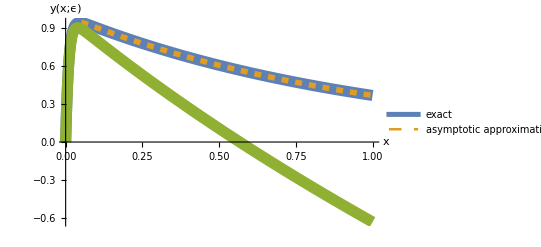

```mathematica
Plot[{y[x]/.NumericalSol,AsymptoticApproxO1[x,0.01],AsymptoticApproxO2[x,0.01]},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01], Directive[Dashed,Thickness[0.01]]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

so it is very interesting that the leading order solution matches really really well with the exact solution, but that the second order approximation does not match well with the exact solution. So i think the moral of the story in this case is that going higher in order does not necessary provide a better approximation to the problem.